```mathematica
SetDirectory["./Desktop/PowerGraphene/BilayerNumDiag"]
```

/home/user/Desktop/PowerGraphene/BilayerNumDiag

## L0

```mathematica
dataL0=Import["fileL0.txt","Table"];
dataL0//MatrixForm
```

(1 | 4. | 2.92152×10^-8 | 7.89142×10^-11
1 | 3.33333 | 4.16824×10^-7 | 3.81478×10^-9
1 | 2.85714 | 2.78958×10^-6 | 4.01354×10^-8
1 | 2.5 | 0.0000120918 | 2.46623×10^-8
1 | 2.22222 | 0.0000367784 | 1.39409×10^-7
1 | 2. | 0.0000905161 | 1.11035×10^-7
2 | 4. | 7.13223×10^-9 | 5.98033×10^-11
2 | 3.33333 | 1.02927×10^-7 | 1.36963×10^-9
2 | 2.85714 | 7.179×10^-7 | 2.15358×10^-9
2 | 2.5 | 2.99848×10^-6 | 1.19969×10^-8
2 | 2.22222 | 9.23142×10^-6 | 1.73632×10^-8
2 | 2. | 0.0000225623 | 4.26516×10^-8
3 | 4. | 3.15043×10^-9 | 3.07837×10^-11
3 | 3.33333 | 4.68115×10^-8 | 2.32342×10^-10
3 | 2.85714 | 3.18026×10^-7 | 1.1854×10^-9
3 | 2.5 | 1.3387×10^-6 | 3.75348×10^-9
3 | 2.22222 | 4.09552×10^-6 | 9.31767×10^-9
3 | 2. | 0.0000100257 | 1.92782×10^-8
5 | 4. | 1.13815×10^-9 | 5.36147×10^-12
5 | 3.33333 | 1.67524×10^-8 | 9.92958×10^-11
5 | 2.85714 | 1.09754×10^-7 | 1.78933×10^-9
5 | 2.5 | 4.67946×10^-7 | 4.88222×10^-9
5 | 2.22222 | 1.45688×10^-6 | 6.45845×10^-9
5 | 2. | 3.56891×10^-6 | 1.65192×10^-8
7 | 4. | 5.48481×10^-10 | 1.57492×10^-11
7 | 3.33333 | 8.46152×10^-9 | 7.36518×10^-11
7 | 2.85714 | 5.79094×10^-8 | 3.12619×10^-10
7 | 2.5 | 2.44125×10^-7 | 1.06439×10^-9
7 | 2.22222 | 7.47993×10^-7 | 2.63191×10^-9
7 | 2. | 1.83301×10^-6 | 5.37979×10^-9
10 | 4. | 2.59171×10^-10 | 1.0806×10^-11
10 | 3.33333 | 4.06583×10^-9 | 5.98882×10^-11
10 | 2.85714 | 2.81035×10^-8 | 2.2815×10^-10
10 | 2.5 | 1.19031×10^-7 | 6.58314×10^-10
10 | 2.22222 | 3.64543×10^-7 | 5.58986×10^-10
10 | 2. | 8.95646×10^-7 | 3.18477×10^-9)

```mathematica
dataL0[[All,3]]/dataL0[[All,4]]//MatrixForm
```

(370.215
109.266
69.5042
490.294
263.817
815.201
119.262
75.1493
333.352
249.938
531.665
528.992
102.341
201.477
268.286
356.655
439.543
520.056
212.284
168.712
61.3377
95.8471
225.578
216.046
34.8261
114.885
185.24
229.357
284.201
340.722
23.9839
67.8903
123.18
180.812
652.151
281.228)

```mathematica
ScientificForm[TableForm[dataL0]]
```

1 | 4. | 2.92152×10^-8 | 7.89142×10^-11
1 | 3.33333 | 4.16824×10^-7 | 3.81478×10^-9
1 | 2.85714 | 2.78958×10^-6 | 4.01354×10^-8
1 | 2.5 | 1.20918×10^-5 | 2.46623×10^-8
1 | 2.22222 | 3.67784×10^-5 | 1.39409×10^-7
1 | 2. | 9.05161×10^-5 | 1.11035×10^-7
2 | 4. | 7.13223×10^-9 | 5.98033×10^-11
2 | 3.33333 | 1.02927×10^-7 | 1.36963×10^-9
2 | 2.85714 | 7.179×10^-7 | 2.15358×10^-9
2 | 2.5 | 2.99848×10^-6 | 1.19969×10^-8
2 | 2.22222 | 9.23142×10^-6 | 1.73632×10^-8
2 | 2. | 2.25623×10^-5 | 4.26516×10^-8
3 | 4. | 3.15043×10^-9 | 3.07837×10^-11
3 | 3.33333 | 4.68115×10^-8 | 2.32342×10^-10
3 | 2.85714 | 3.18026×10^-7 | 1.1854×10^-9
3 | 2.5 | 1.3387×10^-6 | 3.75348×10^-9
3 | 2.22222 | 4.09552×10^-6 | 9.31767×10^-9
3 | 2. | 1.00257×10^-5 | 1.92782×10^-8
5 | 4. | 1.13815×10^-9 | 5.36147×10^-12
5 | 3.33333 | 1.67524×10^-8 | 9.92958×10^-11
5 | 2.85714 | 1.09754×10^-7 | 1.78933×10^-9
5 | 2.5 | 4.67946×10^-7 | 4.88222×10^-9
5 | 2.22222 | 1.45688×10^-6 | 6.45845×10^-9
5 | 2. | 3.56891×10^-6 | 1.65192×10^-8
7 | 4. | 5.48481×10^-10 | 1.57492×10^-11
7 | 3.33333 | 8.46152×10^-9 | 7.36518×10^-11
7 | 2.85714 | 5.79094×10^-8 | 3.12619×10^-10
7 | 2.5 | 2.44125×10^-7 | 1.06439×10^-9
7 | 2.22222 | 7.47993×10^-7 | 2.63191×10^-9
7 | 2. | 1.83301×10^-6 | 5.37979×10^-9
10 | 4. | 2.59171×10^-10 | 1.0806×10^-11
10 | 3.33333 | 4.06583×10^-9 | 5.98882×10^-11
10 | 2.85714 | 2.81035×10^-8 | 2.2815×10^-10
10 | 2.5 | 1.19031×10^-7 | 6.58314×10^-10
10 | 2.22222 | 3.64543×10^-7 | 5.58986×10^-10
10 | 2. | 8.95646×10^-7 | 3.18477×10^-9

```mathematica
dataL0[[1;;6,2;;3]]//MatrixForm
dataL0[[1;;6,4]]//MatrixForm
```

(4. | 2.92152×10^-8
3.33333 | 4.16824×10^-7
2.85714 | 2.78958×10^-6
2.5 | 0.0000120918
2.22222 | 0.0000367784
2. | 0.0000905161)

(7.89142×10^-11
3.81478×10^-9
4.01354×10^-8
2.46623×10^-8
1.39409×10^-7
1.11035×10^-7)

```mathematica
NonlinearModelFit[dataL0[[01;;06,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[01;;06,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[07;;12,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[07;;12,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[13;;18,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[13;;18,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[19;;24,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[19;;24,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[25;;30,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[25;;30,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL0[[31;;36,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL0[[31;;36,4]]^2][{"BestFit","ParameterTable"}]
```

{0.280496 ⅇ^(-4.02004 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.280496 | 0.00196419 | 142.805 | 1.44223×10^-8
G | 4.02004 | 0.00283843 | 1416.29 | 1.49122×10^-12}

{0.0711557 ⅇ^(-4.02785 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0711557 | 0.000621435 | 114.502 | 3.48877×10^-8
G | 4.02785 | 0.00374853 | 1074.52 | 4.50088×10^-12}

{0.0315756 ⅇ^(-4.02743 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0315756 | 0.000138079 | 228.679 | 2.19378×10^-9
G | 4.02743 | 0.00183883 | 2190.21 | 2.60738×10^-13}

{0.0111328 ⅇ^(-4.02387 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0111328 | 0.000129866 | 85.7254 | 1.10999×10^-7
G | 4.02387 | 0.00400248 | 1005.34 | 5.8734×10^-12}

{0.0058615 ⅇ^(-4.0348 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0058615 | 0.0000584082 | 100.354 | 5.91186×10^-8
G | 4.0348 | 0.0042511 | 949.119 | 7.39377×10^-12}

{0.00291686 ⅇ^(-4.04418 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00291686 | 0.0000402462 | 72.4754 | 2.17189×10^-7
G | 4.04418 | 0.00615053 | 657.533 | 3.20977×10^-11}

```mathematica
G0L0=({{1, 4.020037237964663, 0.0028384283480775365}, {2, 4.027850346601865, 0.0037485254880071693}, {3, 4.027431524370874, 0.0018388306247344470}, {5, 4.023866143435842, 0.0040024767255463100}, {7, 4.034798551331821, 0.0042511001116005975}, {10, 4.044175706964364, 0.0061505288902013325}});
```

```mathematica
Export["G0L0.txt",G0L0,"Table"]
```

G0L0.txt

```mathematica
G0L0[[All,3]]
```

{0.00283843,0.00374853,0.00183883,0.00400248,0.0042511,0.00615053}

```mathematica
Needs["LinearRegression`"]
Regress[{{1, 4.032313105777002}, {2, 4.027850346601865}, {3, 4.027431524370874}, {5, 4.06301052826296}, {7, 4.034798551331821}, {10, 4.044175706964364}},{1,x},x,RegressionReport->{RSquared}]
```

General::obspkg: LinearRegression` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

{RSquared→0.186964}

```mathematica
NonlinearModelFit[G0L0[[All,1;;2]],A+α a,{A,α},{a},Weights->1/G0L0[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{4.01999+0.00210989 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 4.01999 | 0.00255665 | 1572.37 | 9.81598×10^-13
α | 0.00210989 | 0.000644822 | 3.27205 | 0.0307296}

```mathematica
ScientificForm[0.002109893534338766/4.019988578532697]
```

5.24851×10^-4

```mathematica
ScientificForm[{{0.0018968864057580992, 0.0008720075486863968}}]
```

{{1.89689×10^-3,8.72008×10^-4}}

```mathematica
4.02297508877706/0.0036774851652854753
0.0018968864057580992/0.0008720075486863968
```

1093.95

2.17531

```mathematica
Manipulate[Show[ListPlot[G0L0[[All,1;;2]],AspectRatio->1,PlotRange->All],Plot[(4.019988578532697+0.0036774851652854753α)+(0.002109893534338766+0.0008720075486863968β) a,{a,0,10},PlotRange->All],Plot[{(4.019988578532697+0.0036774851652854753(-1))+(0.002109893534338766+0.0008720075486863968(-1)) a,(4.019988578532697+0.0036774851652854753(+1))+(0.002109893534338766+0.0008720075486863968(+1)) a},{a,0,10},Filling->{1-> {2}}]],{{α,0},-1,1},{{β,0},-1,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

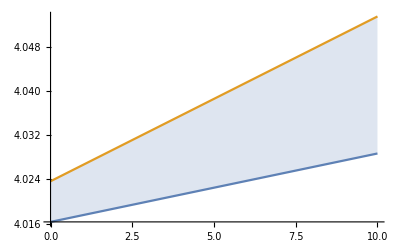

```mathematica
Plot[{(4.019988578532697+0.0036774851652854753(-1))+(0.002109893534338766+0.0008720075486863968(-1)) a,(4.019988578532697+0.0036774851652854753(+1))+(0.002109893534338766+0.0008720075486863968(+1)) a},{a,0,10},Filling->{1-> {2}}]
```

```mathematica
C0L0=({{1, 0.28049596064524174, 0.0019641867046810476}, {2, 0.07115574062511905, 0.0006214347853378486}, {3, 0.03157564332898384, 0.0001380787077899456}, {5, 0.011132807020840718, 0.00012986597508196597}, {7, 0.005861502382714182, 0.00005840823852944507}, {10, 0.0029168555089081494, 0.00004024616068829552}});
```

```mathematica
Export["C0L0.txt",C0L0,"Table"]
```

C0L0.txt

```mathematica
C0L0[[All,3]]
```

{0.00196419,0.000621435,0.000138079,0.000129866,0.0000584082,0.0000402462}

```mathematica
NonlinearModelFit[C0L0[[All,1;;2]],(A/a)^α,{A,α},{a},Weights->1/C0L0[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{0.280788 (1/a)^1.98966, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.528149 | 0.00291596 | 181.124 | 5.57395×10^-9
α | 1.98966 | 0.00621368 | 320.207 | 5.70692×10^-10}

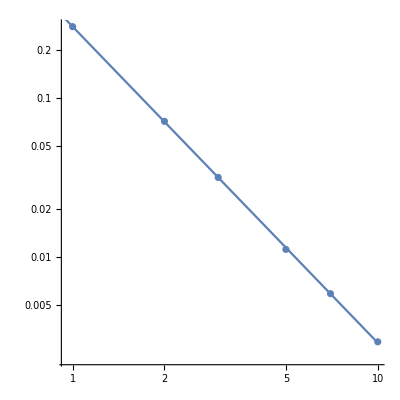

```mathematica
Show[ListLogLogPlot[C0L0[[All,1;;2]],AspectRatio->1],LogLogPlot[0.2807881109181846 (1/a)^1.9896615293714222,{a,0,10}]]
```

```mathematica
NonlinearModelFit[dataL0[[All,1;;3]],(A^2 ⅇ^(-G ginv))/a^2,{G,A},{a,ginv},Weights->1/dataL0[[All,4]]^2][{"BestFit","ParameterTable"}]
```

{(0.281561 ⅇ^(-4.02406 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
G | 4.02406 | 0.00241646 | 1665.27 | 4.34056×10^-85
A | 0.530623 | 0.00154074 | 344.394 | 8.05741×10^-62}

```mathematica
{(0.28571990773748085 ⅇ^(-4.030750613579991 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.030750613579991, 0.0032913115094340595, 1224.6639681556844, 1.4976510024368249*^-80}, {A, 0.5345277427201331, 0.0020041463256844265, 266.7109361576127, 4.778937116762248*^-58}}};
```

## L2

```mathematica
dataL2=Import["fileL2.txt","Table"];
dataL2//MatrixForm
```

(1 | 2. | 2.7127×10^-8 | 5.88125×10^-11
1 | 1.66667 | 3.95448×10^-7 | 1.19738×10^-9
1 | 1.42857 | 2.68217×10^-6 | 5.84284×10^-9
1 | 1.25 | 0.0000112794 | 1.93078×10^-8
1 | 1.11111 | 0.0000345039 | 4.93224×10^-8
2 | 2. | 6.55098×10^-9 | 5.27816×10^-11
2 | 1.66667 | 9.81992×10^-8 | 4.53553×10^-10
2 | 1.42857 | 6.67918×10^-7 | 2.03009×10^-9
2 | 1.25 | 2.8119×10^-6 | 6.55875×10^-9
2 | 1.11111 | 8.60731×10^-6 | 1.64221×10^-8
3 | 2. | 2.92241×10^-9 | 2.95438×10^-11
3 | 1.66667 | 4.34776×10^-8 | 2.2435×10^-10
3 | 1.42857 | 2.9587×10^-7 | 1.117×10^-9
3 | 1.25 | 1.24681×10^-6 | 3.54743×10^-9
3 | 1.11111 | 3.81851×10^-6 | 8.81845×10^-9
5 | 2. | 1.04595×10^-9 | 4.64577×10^-12
5 | 1.66667 | 1.55836×10^-8 | 8.60915×10^-11
5 | 1.42857 | 1.0589×10^-7 | 5.43316×10^-10
5 | 1.25 | 4.47072×10^-7 | 1.66031×10^-9
5 | 1.11111 | 1.37043×10^-6 | 4.09091×10^-9
7 | 2. | 5.05321×10^-10 | 1.51382×10^-11
7 | 1.66667 | 7.84517×10^-9 | 7.5651×10^-11
7 | 1.42857 | 5.38602×10^-8 | 2.97605×10^-10
7 | 1.25 | 2.27356×10^-7 | 1.00044×10^-9
7 | 1.11111 | 6.97338×10^-7 | 2.48916×10^-9
10 | 2. | 2.42988×10^-10 | 8.00953×10^-12
10 | 1.66667 | 3.78447×10^-9 | 5.33048×10^-11
10 | 1.42857 | 2.61431×10^-8 | 2.13215×10^-10
10 | 1.25 | 1.10834×10^-7 | 6.2397×10^-10
10 | 1.11111 | 3.40468×10^-7 | 1.48889×10^-9)

```mathematica
dataL2[[All,3]]/dataL2[[All,4]]//MatrixForm
```

(461.246
330.261
459.053
584.187
699.559
124.115
216.511
329.008
428.725
524.131
98.9178
193.794
264.878
351.468
433.014
225.141
181.012
194.895
269.27
334.994
33.3805
103.702
180.979
227.256
280.15
30.3374
70.9967
122.614
177.627
228.673)

```mathematica
dataL2[[All,3]]+a dataL2[[All,4]]
```

```mathematica
ScientificForm[TableForm[{dataL2[[All,1]],dataL2[[All,2]],dataL2[[All,3]]+a dataL2[[All,4]]}ᵀ]]
```

1 | 2. | 2.7127×10^-8+(5.88125×10^-11) a
1 | 1.66667 | 3.95448×10^-7+(1.19738×10^-9) a
1 | 1.42857 | 2.68217×10^-6+(5.84284×10^-9) a
1 | 1.25 | 1.12794×10^-5+(1.93078×10^-8) a
1 | 1.11111 | 3.45039×10^-5+(4.93224×10^-8) a
2 | 2. | 6.55098×10^-9+(5.27816×10^-11) a
2 | 1.66667 | 9.81992×10^-8+(4.53553×10^-10) a
2 | 1.42857 | 6.67918×10^-7+(2.03009×10^-9) a
2 | 1.25 | 2.8119×10^-6+(6.55875×10^-9) a
2 | 1.11111 | 8.60731×10^-6+(1.64221×10^-8) a
3 | 2. | 2.92241×10^-9+(2.95438×10^-11) a
3 | 1.66667 | 4.34776×10^-8+(2.2435×10^-10) a
3 | 1.42857 | 2.9587×10^-7+(1.117×10^-9) a
3 | 1.25 | 1.24681×10^-6+(3.54743×10^-9) a
3 | 1.11111 | 3.81851×10^-6+(8.81845×10^-9) a
5 | 2. | 1.04595×10^-9+(4.64577×10^-12) a
5 | 1.66667 | 1.55836×10^-8+(8.60915×10^-11) a
5 | 1.42857 | 1.0589×10^-7+(5.43316×10^-10) a
5 | 1.25 | 4.47072×10^-7+(1.66031×10^-9) a
5 | 1.11111 | 1.37043×10^-6+(4.09091×10^-9) a
7 | 2. | 5.05321×10^-10+(1.51382×10^-11) a
7 | 1.66667 | 7.84517×10^-9+(7.5651×10^-11) a
7 | 1.42857 | 5.38602×10^-8+(2.97605×10^-10) a
7 | 1.25 | 2.27356×10^-7+(1.00044×10^-9) a
7 | 1.11111 | 6.97338×10^-7+(2.48916×10^-9) a
10 | 2. | 2.42988×10^-10+(8.00953×10^-12) a
10 | 1.66667 | 3.78447×10^-9+(5.33048×10^-11) a
10 | 1.42857 | 2.61431×10^-8+(2.13215×10^-10) a
10 | 1.25 | 1.10834×10^-7+(6.2397×10^-10) a
10 | 1.11111 | 3.40468×10^-7+(1.48889×10^-9) a

```mathematica
dataL2[[1;;6,2;;3]]//MatrixForm
dataL2[[1;;6,4]]//MatrixForm
```

(2. | 2.7127×10^-8
1.66667 | 3.95448×10^-7
1.42857 | 2.68217×10^-6
1.25 | 0.0000112794
1.11111 | 0.0000345039
2. | 6.55098×10^-9)

(5.88125×10^-11
1.19738×10^-9
5.84284×10^-9
1.93078×10^-8
4.93224×10^-8
5.27816×10^-11)

```mathematica
NonlinearModelFit[dataL2[[01;;05,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[01;;05,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[06;;10,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[06;;10,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[11;;15,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[11;;15,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[16;;20,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[16;;20,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[21;;25,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[21;;25,4]]^2][{"BestFit","ParameterTable"}]
NonlinearModelFit[dataL2[[26;;30,2;;3]],A ⅇ^(-G ginv),{A,G},{ginv},Weights->1/dataL2[[26;;30,4]]^2][{"BestFit","ParameterTable"}]
```

{0.261929 ⅇ^(-8.04183 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.261929 | 0.000439774 | 595.599 | 1.04377×10^-8
G | 8.04183 | 0.00118833 | 6767.34 | 7.1157×10^-12}

{0.0669686 ⅇ^(-8.06257 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0669686 | 0.000729218 | 91.8361 | 2.84606×10^-6
G | 8.06257 | 0.0084716 | 951.718 | 2.55826×10^-9}

{0.0296686 ⅇ^(-8.06177 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0296686 | 0.000194117 | 152.839 | 6.17592×10^-7
G | 8.06177 | 0.00507877 | 1587.35 | 5.51385×10^-10}

{0.0107854 ⅇ^(-8.07279 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0107854 | 0.0000768966 | 140.258 | 7.99107×10^-7
G | 8.07279 | 0.0049972 | 1615.46 | 5.23094×10^-10}

{0.00554784 ⅇ^(-8.08231 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00554784 | 0.000100733 | 55.0747 | 0.0000131856
G | 8.08231 | 0.0143748 | 562.253 | 1.24071×10^-8}

{0.00278251 ⅇ^(-8.10605 ginv), | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00278251 | 0.000056224 | 49.4898 | 0.0000181671
G | 8.10605 | 0.016242 | 499.079 | 1.77401×10^-8}

```mathematica
G0L2=({{1, 8.041832777558335, 0.0011883306349949082}, {2, 8.06256602900104, 0.0084715956691226950}, {3, 8.061769210078928, 0.0050787717215021920}, {5, 8.07279348163923, 0.0049972022054462625}, {7, 8.082306098602958, 0.0143748435730100250}, {10, 8.106047313745172, 0.0162420193382868260}});
```

```mathematica
Export["G0L2.txt",G0L2,"Table"]
```

G0L2.txt

```mathematica
Needs["LinearRegression`"]
Regress[{{1, 8.041832777558335}, {2, 8.06256602900104}, {3, 8.061769210078928}, {5, 8.07279348163923}, {7, 8.082306098602958}, {10, 8.106047313745172}},{1,x},x,RegressionReport->{RSquared}]
```

General::obspkg: LinearRegression` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RSquared::shdw: Symbol RSquared appears in multiple contexts {RegressionCommon`,Global`}; definitions in context RegressionCommon` may shadow or be shadowed by other definitions.

{RSquared→0.948556}

```mathematica
NonlinearModelFit[G0L2[[All,1;;2]],A+α a,{A,α},{a},Weights->1/G0L2[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{8.03441+0.00778221 a, | Estimate | Standard Error | t-Statistic | P-Value
A | 8.03441 | 0.00154081 | 5214.4 | 8.11584×10^-15
α | 0.00778221 | 0.000839023 | 9.27532 | 0.000751466}

```mathematica
ScientificForm[0.0077822086177004295/8.034410086348137]
```

9.6861×10^-4

```mathematica
ScientificForm[{{0.0077822086177004295, 0.0008390232365048055}}]
```

{{7.78221×10^-3,8.39023×10^-4}}

```mathematica
8.034410086348137/0.001540811617299269
0.0077822086177004295/0.0008390232365048055
```

5214.4

9.27532

```mathematica
Manipulate[Show[ListPlot[G0L2[[All,1;;2]],AspectRatio->1,PlotRange->All],Plot[(8.034410086348137+0.001540811617299269α)+(0.0077822086177004295+0.0008390232365048055β) a,{a,0,10},PlotRange->All],Plot[{(8.034410086348137+0.001540811617299269(-1))+(0.0077822086177004295+0.0008390232365048055(-1)) a,(8.034410086348137+0.001540811617299269(+1))+(0.0077822086177004295+0.0008390232365048055(+1)) a,
(8.034410086348137+0.001540811617299269(-2))+(0.0077822086177004295+0.0008390232365048055(-2)) a,(8.034410086348137+0.001540811617299269(+3))+(0.0077822086177004295+0.0008390232365048055(+3)) a},{a,0,10},Filling->{1-> {2},2-> {4},1-> {3}}],FillingStyle->{Red,Green,Blue}],{{α,0},-1,1},{{β,0},-1,1}]
```

```mathematica
C0L2=({{1, 0.26192867507438883, 0.00043977371615375676}, {2, 0.06696857669536116, 0.0007292181211831182}, {3, 0.029668617661489177, 0.0001941168380948426}, {5, 0.010785389667344533, 0.0000768965777220101}, {7, 0.00554783572302413, 0.00010073290880814306}, {10, 0.0027825148394452753, 0.00005622401983145206}});
```

```mathematica
Export["C0L2.txt",C0L2,"Table"]
```

C0L2.txt

```mathematica
1000C0L2//MatrixForm
G0L2//MatrixForm
```

(1000 | 261.929 | 0.439774
2000 | 66.9686 | 0.729218
3000 | 29.6686 | 0.194117
5000 | 10.7854 | 0.0768966
7000 | 5.54784 | 0.100733
10000 | 2.78251 | 0.056224)

(1 | 8.04183 | 0.00118833
2 | 8.06257 | 0.0084716
3 | 8.06177 | 0.00507877
5 | 8.07279 | 0.0049972
7 | 8.08231 | 0.0143748
10 | 8.10605 | 0.016242)

```mathematica
NonlinearModelFit[C0L2[[All,1;;2]],(A/a)^α,{A,α},{a},Weights->1/C0L2[[All,3]]^2][{"BestFit","ParameterTable"}]
```

{0.261936 (1/a)^1.98052, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.508436 | 0.000499265 | 1018.37 | 5.57865×10^-12
α | 1.98052 | 0.00198037 | 1000.07 | 5.99824×10^-12}

```mathematica
Manipulate[Show[ListLogLogPlot[C0L2[[All,1;;2]],AspectRatio->1],LogLogPlot[ ((0.5084356242792902+0.0004992649201494674α)/a)^(1.980515652731696+0.001980373669386424β),{a,0,10}]],{α,-1,1},{β,-1,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLogLogPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLogLogPlot[Symbol[],AspectRatio→1],].

```mathematica
NonlinearModelFit[dataL2[[All,1;;3]],(A^2 ⅇ^(-G ginv))/a^2,{G,A},{a,ginv},Weights->1/dataL2[[All,4]]^2][{"BestFit","ParameterTable"}]
```

{(0.2637 ⅇ^(-8.05038 ginv))/a^2, | Estimate | Standard Error | t-Statistic | P-Value
G | 8.05038 | 0.00508591 | 1582.88 | 7.08087×10^-71
A | 0.513518 | 0.00177189 | 289.814 | 3.11459×10^-50}

# Comparing L0 and L2

```mathematica
{(0.28571990773748085 ⅇ^(-4.030750613579991 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.030750613579991, 0.0032913115094340595, 1224.6639681556844, 1.4976510024368249*^-80}, {A, 0.5345277427201331, 0.0020041463256844265, 266.7109361576127, 4.778937116762248*^-58}}};
{(0.2637004421506521 ⅇ^(-8.050383600102412 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 8.050383600102412, 0.005085908841636671, 1582.88004185143, 7.080874644491508*^-71}, {A, 0.5135177135704786, 0.001771887916950576, 289.81388080925797, 3.114587677034216*^-50}}};
```

```mathematica
{0.28260486459800893 (1/a)^1.9914039761429185,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 0.53015798551308, 0.0040912534285322925, 129.58326702906555, 2.1270766819199266*^-8}, {α, 1.9914039761429185, 0.008251788486610265, 241.32998311508624, 1.768709094552371*^-9}}};
{0.2619363341408044 (1/a)^1.980515652731696,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 0.5084356242792902, 0.0004992649201494674, 1018.3684127598578, 5.578645672554518*^-12}, {α, 1.980515652731696, 0.001980373669386424, 1000.0716952297776, 5.9982396402658956*^-12}}};
```

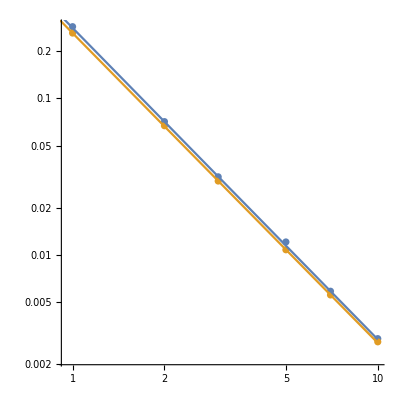

```mathematica
Show[ListLogLogPlot[{C0L0[[All,1;;2]],C0L2[[All,1;;2]]},AspectRatio->1],LogLogPlot[{0.28260486459800893 (1/a)^1.9914039761429185,0.2619363341408044 (1/a)^1.980515652731696},{a,0,10}]]
```

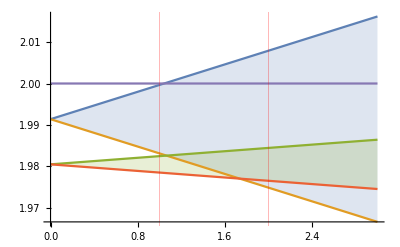

```mathematica
Plot[{1.9914039761429185+0.008251788486610265x,1.9914039761429185-0.008251788486610265x,1.980515652731696+0.001980373669386424x,1.980515652731696-0.001980373669386424x,2},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
{4.02297508877706+0.0018968864057580992 a,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 4.02297508877706, 0.0036774851652854753, 1093.9473330179335, 4.189509462772544*^-12}, {α, 0.0018968864057580992, 0.0008720075486863968, 2.17530961585779, 0.09524266752803368}}};
{8.034410086348137+0.0077822086177004295 a,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {A, 8.034410086348137, 0.001540811617299269, 5214.401290944854, 8.115837473546208*^-15}, {α, 0.0077822086177004295, 0.0008390232365048055, 9.275319537179298, 0.0007514663847588728}}};
```

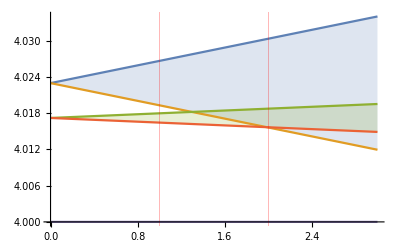

```mathematica
Plot[{4.02297508877706+0.0036774851652854753x,4.02297508877706-0.0036774851652854753x,(8.034410086348137+0.001540811617299269x)/2,(8.034410086348137-0.001540811617299269x)/2,4},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
{(0.2815610830507133 ⅇ^(-4.02406099634526 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 4.02406099634526, 0.0024164555528118016, 1665.274162259198, 4.34056254690846*^-85}, {A, 0.5306232967470551, 0.0015407441631660737, 344.39416317935473, 8.057408449328595*^-62}}};
{(0.2637004421506521 ⅇ^(-8.050383600102412 ginv))/a^2,{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {G, 8.050383600102412, 0.005085908841636671, 1582.88004185143, 7.080874644491508*^-71}, {A, 0.5135177135704786, 0.001771887916950576, 289.81388080925797, 3.114587677034216*^-50}}};
```

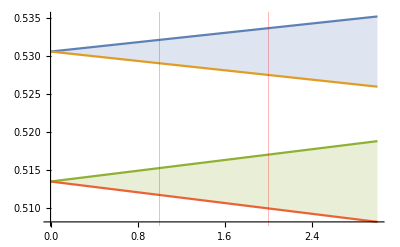

```mathematica
Plot[{0.5306232967470551+0.0015407441631660737x,0.5306232967470551-0.0015407441631660737x,0.5135177135704786+0.001771887916950576x,0.5135177135704786-0.001771887916950576x},{x,0,3},Filling->{1-> {2},3-> {4}},GridLines->{{{1,Red},{2,Red}},None}]
```

```mathematica
4.02406099634526+±0.0024164555528118016
8.050383600102412/2±0.005085908841636671/2
```

4.02406+±0.00241646

4.02519±0.00254295

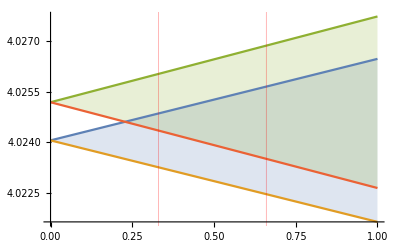

```mathematica
Plot[{4.02406099634526+0.0024164555528118016x,4.02406099634526-0.0024164555528118016x,(8.050383600102412+0.005085908841636671x)/2,(8.050383600102412-0.005085908841636671x)/2},{x,0,1},Filling->{1-> {2},3-> {4}},GridLines->{{{.33,Red},{.66,Red}},None}]
```

```mathematica
Manipulate[Plot[{b-a/x,b-a x,b},{x,0.1,10},PlotRange->All],{a,0,+10},{b,0.1,100}]
```